```mathematica
SetDirectory@NotebookDirectory[];
Import["Qubits_package.m"];
Import["ExactKrylov_package.m"];
```

## Parameters

```mathematica
Nq=10;
(*HamType="Heisenberg";*)
HamType="FermiHubbard";
GraphType=ToString[2];
```

```mathematica
Ntrials=20;
logηList=Table[-0.1*j,{j,-50,150}];
PR={{1.*^-3,1.*^12},{1.*^-14,1.*^1}};
```

```mathematica
seed=RandomInteger[{1,1000000}]; 
(*seed=123; *)
SeedRandom[seed];
```

## Run

```mathematica
graphs={};
plotsRTE={};
plotsF={};
plots={};
γ2ϵK={};
```

```mathematica
trial=0;
While[trial<Ntrials,(
Label[begin];

If[StringMatchQ[HamType,"Heisenberg"],(
EL=funGraph[Nq,GraphType];
Model=funHeisenberg[Nq,EL]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
EL=funGraph[Nq/2,GraphType];
u=1.;
Model=funFermiHubbard[Nq,EL,u]
)];
Ham=funHamiltonianQubit[Model];

{EE,ES}=funSpectrum[Ham];
HamNorm=Max[Abs[EE]];
EE=EE/HamNorm;
Eg=EE[[1]];
If[StringMatchQ[HamType,"Heisenberg"],(
htot=3.*Length[EL]/HamNorm
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
htot=(2.*Length[EL]+u/4.*Nq/2.)/HamNorm
)];

If[StringMatchQ[HamType,"Heisenberg"],(
ψ=funPairwiseSinglet[Nq]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
ψ=funHartreeFock[Nq,EL]
)];
ψ=Conjugate[ES].ψ;
ψ=Flatten[ψ];
Proψ=Abs[ψ]^2;
pg=Proψ[[1]];
ER=Total[Proψ*EE];
ϵR=ER-Eg;

If[pg<1.*^-3,(
Print[pg];
Goto[begin];
)];

d=RandomChoice[Table[i,{i,2,30}]];
Ide=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatPower[EE,Proψ,d,E0];
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg;
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
ϵK=EK-Eg;
If[ϵK>1.*^-2||ϵK<1.*^-9,(
Print[{d,ϵK}];
Goto[begin];
)];
AppendTo[graphs,Graph[EL]];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListP=γList;
ϵListP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γP=γ;

E0=0;
{Hmat,Smat}=funMatChebyshev[EE,Proψ,d,htot,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListCP=γList;
ϵListCP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γCP=γ;

E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,1,htot,τ,E0];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;
δ=RandomReal[{-0.1,0.1}];
E0=Eg+δ;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,d,htot,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,htot,1.,logηList];
γListGP=γList;
ϵListGP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γGP=γ;

E0=Eg-1.;
{Hmat,Smat}=funMatInversePower[EE,Proψ,d,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListIP=γList;
ϵListIP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γIP=γ;

E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;
E0=Eg;
{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListITE=γList;
ϵListITE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γITE=γ;

ΔtList=Table[(2.*PI)/100 j,{j,1,100}];
ϵKList=ΔtList;
Do[(
Δt=ΔtList[[j]];

E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err
),{j,1,Length[ΔtList]}];
Δt=ΔtList[[Position[ϵKList,Min[ϵKList]][[1,1]]]];
AppendTo[plotsRTE,ListLogPlot[Transpose[{ΔtList,ϵKList}],PlotRange->Full]];
E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListRTE=γList;
ϵListRTE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γRTE=γ;

ΔE=0.;
E0=Eg;
τMIN=0;
τMAX=64;
Do[(
T=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=T];
If[err<ϵB,τMAX=T];
),{j,1,30}];
T=(τMIN+τMAX)/2.;
ΔEList=Table[2./(d*100)*j,{j,1,100}];
ϵKList=ΔEList;
Do[(
ΔE=ΔEList[[j]];

E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err;
),{j,1,Length[ΔEList]}];
ΔE=ΔEList[[Position[ϵKList,Min[ϵKList]][[1,1]]]];
AppendTo[plotsF,ListLogPlot[Transpose[{ΔEList,ϵKList}],PlotRange->Full]];
E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListF=γList;
ϵListF=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γF=γ;

AppendTo[plots,ListLogLogPlot[{Transpose[{γListP,0.*ϵListP+ϵK}],Transpose[{γListP,0.*ϵListP+2.*ϵK}],Transpose[{γListP,ϵListP}],Transpose[{γListCP,ϵListCP}],Transpose[{γListGP,ϵListGP}],Transpose[{γListIP,ϵListIP}],Transpose[{γListITE,ϵListITE}],Transpose[{γListRTE,ϵListRTE}],Transpose[{γListF,ϵListF}]},PlotRange->PR,Joined->True,PlotStyle->{Cyan,Brown,Red,Yellow,Blue,Green,Orange,Purple,Magenta}]];

AppendTo[γ2ϵK,{γP,γCP,γGP,γIP,γITE,γRTE,γF}];
trial=trial+1;
Print[{"trial",trial,"d",d,ϵK,ToString[Now]}];
)]
γ2ϵK=Transpose[γ2ϵK];
```

0.000884787

{trial,1,d,26,1.33344×10^-6,DateObject[{2022, 12, 10, 12, 51, 44.9405384}, Instant, Gregorian, 8.]}

{trial,2,d,8,0.0000190524,DateObject[{2022, 12, 10, 12, 51, 49.4416469}, Instant, Gregorian, 8.]}

{trial,3,d,5,0.00416199,DateObject[{2022, 12, 10, 12, 51, 53.1100486}, Instant, Gregorian, 8.]}

{trial,4,d,22,3.29341×10^-8,DateObject[{2022, 12, 10, 12, 52, 6.8247180}, Instant, Gregorian, 8.]}

{5,0.0131779}

{trial,5,d,20,1.60191×10^-6,DateObject[{2022, 12, 10, 12, 52, 21.1978405}, Instant, Gregorian, 8.]}

{trial,6,d,11,0.000082384,DateObject[{2022, 12, 10, 12, 52, 26.6665544}, Instant, Gregorian, 8.]}

{trial,7,d,14,4.94516×10^-8,DateObject[{2022, 12, 10, 12, 52, 33.7712455}, Instant, Gregorian, 8.]}

{2,0.0145355}

{trial,8,d,17,9.69769×10^-8,DateObject[{2022, 12, 10, 12, 52, 45.7116394}, Instant, Gregorian, 8.]}

{trial,9,d,3,0.00244131,DateObject[{2022, 12, 10, 12, 52, 49.2490670}, Instant, Gregorian, 8.]}

{trial,10,d,13,0.000588465,DateObject[{2022, 12, 10, 12, 52, 55.7405939}, Instant, Gregorian, 8.]}

{trial,11,d,24,0.00011042,DateObject[{2022, 12, 10, 12, 53, 11.7725325}, Instant, Gregorian, 8.]}

{trial,12,d,20,4.3414×10^-8,DateObject[{2022, 12, 10, 12, 53, 23.4078201}, Instant, Gregorian, 8.]}

{trial,13,d,28,7.50221×10^-6,DateObject[{2022, 12, 10, 12, 53, 47.0080908}, Instant, Gregorian, 8.]}

{2,0.0241691}

{trial,14,d,2,0.00327647,DateObject[{2022, 12, 10, 12, 53, 53.1813887}, Instant, Gregorian, 8.]}

{trial,15,d,9,0.00396963,DateObject[{2022, 12, 10, 12, 53, 58.0045832}, Instant, Gregorian, 8.]}

0.000441786

{5,0.0441659}

{trial,16,d,28,4.34021×10^-6,DateObject[{2022, 12, 10, 12, 54, 27.2765105}, Instant, Gregorian, 8.]}

0.00052126

{trial,17,d,3,0.00567203,DateObject[{2022, 12, 10, 12, 54, 33.5770070}, Instant, Gregorian, 8.]}

{trial,18,d,26,7.83147×10^-8,DateObject[{2022, 12, 10, 12, 54, 54.2416715}, Instant, Gregorian, 8.]}

{trial,19,d,20,1.21933×10^-9,DateObject[{2022, 12, 10, 12, 55, 5.9382695}, Instant, Gregorian, 8.]}

{24,1.22125×10^-14}

{trial,20,d,8,0.0002122,DateObject[{2022, 12, 10, 12, 55, 13.0602143}, Instant, Gregorian, 8.]}

## Plots

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

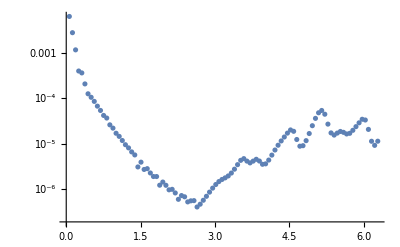
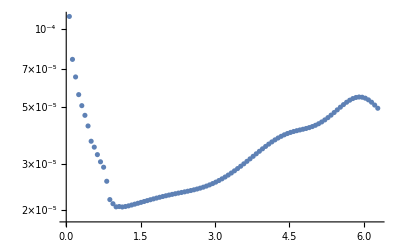
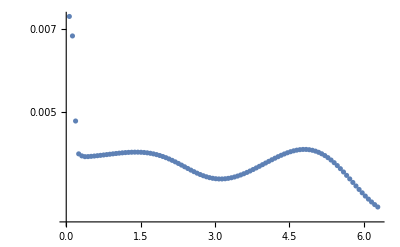
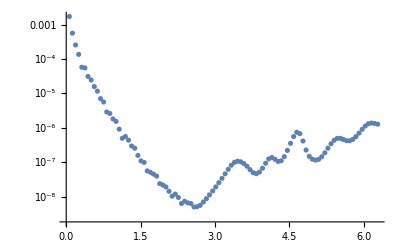
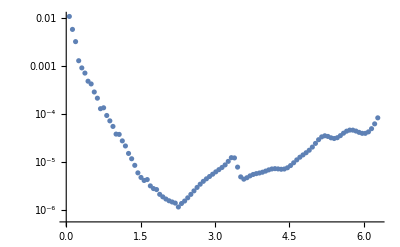
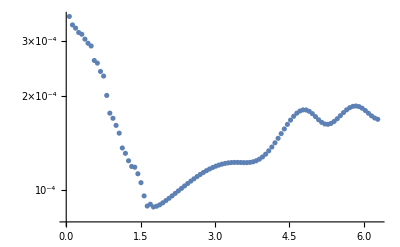
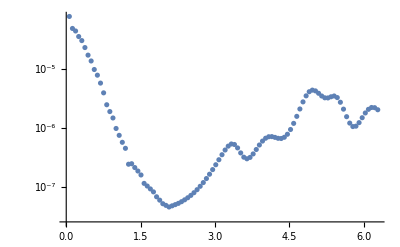
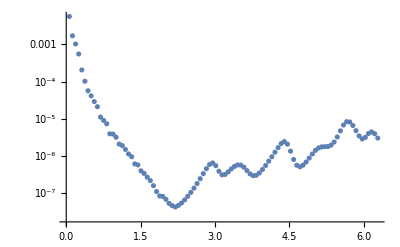

```mathematica
graphs
plotsRTE
plotsF
plots
```

## Data

```mathematica
If[!StringMatchQ[GraphType, "Chain"]&&!StringMatchQ[GraphType, "Ladder"], GraphType="Random"];
```

```mathematica
path=ToString[HamType]<>"-"<>ToString[GraphType]<>"-Nq="<>ToString[Nq]<>"-5.dat";
CreateFile[path];
file=File[path];
```

```mathematica
Data={};
AppendTo[Data,"γ2ϵK:"];
Data=Join[Data,γ2ϵK];
AppendTo[Data,""];
AppendTo[Data,"seed:"];
AppendTo[Data,seed];
AppendTo[Data,""];
Export[file,Data];
```